# Data Set 4

```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/Research/Radiation Thickness/Data";

SetDirectory[main];
$Line=0;

set=4;
```

## Data Import

$SPEC_ID:
Molnar Range
$SPEC_REM:
DET# 1
DETDESC# HPGe Detector 1
AP# GammaVision Version 6.07
$DATE_MEA:
02/03/2016 13:05:24
$MEAS_TIM:
3600 3905
$DATA:
0 8191
       0
       0
       0

0
       0
$ROI:
0
$PRESETS:
Live Time
3600
0
$ENER_FIT:
0.137869 0.366631
$MCA_CAL:
3
1.378689E-001 3.666307E-001 -4.415950E-008 keV
$SHAPE_CAL:
3
2.301834E+000 9.195991E-004 -5.357180E-008

\begin{array}{c}
 \text{$\$$SPEC$\_$ID:} \\
 \text{Molnar Range} \\
 \text{$\$$SPEC$\_$REM:} \\
 \text{DET$\#$ 1} \\
 \text{DETDESC$\#$ HPGe Detector 1} \\
 \text{AP$\#$ GammaVision Version 6.07} \\
 \text{$\$$DATE$\_$MEA:} \\
 \text{02/03/2016 13:05:24} \\
 \text{$\$$MEAS$\_$TIM:} \\
 \text{3600 3905} \\
 \text{$\$$DATA:} \\
 \text{0 8191} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{       0} \\
 \text{$\$$ROI:} \\
 0 \\
 \text{$\$$PRESETS:} \\
 \text{Live Time} \\
 3600 \\
 0 \\
 \text{$\$$ENER$\_$FIT:} \\
 \text{0.137869 0.366631} \\
 \text{$\$$MCA$\_$CAL:} \\
 3 \\
 \text{1.378689E-001 3.666307E-001 -4.415950E-008 keV} \\
 \text{$\$$SHAPE$\_$CAL:} \\
 3 \\
 \text{2.301834E+000 9.195991E-004 -5.357180E-008} \\
\end{array}

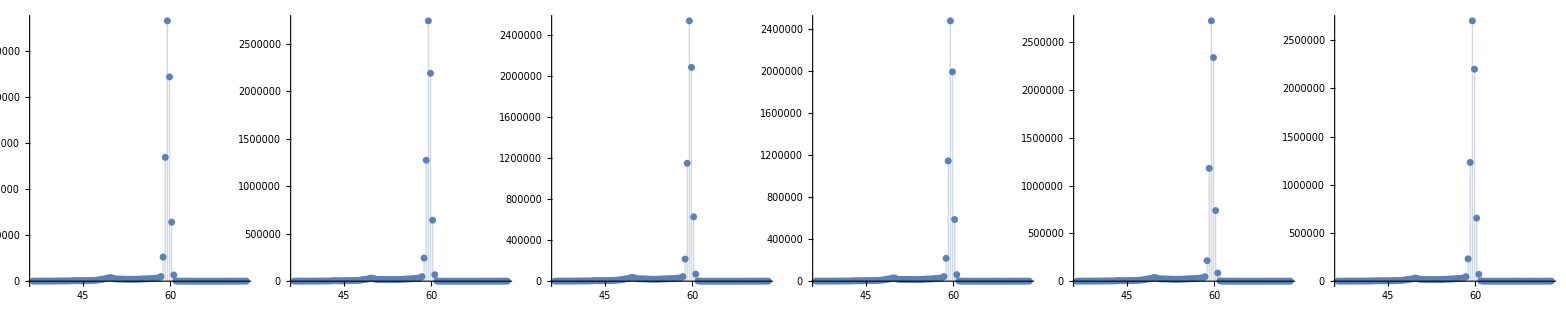

```mathematica
filenames={
"Run 1 - Am-241-1hr-NewConfiguration.Spe",
"Run 2 - Am-241-1hr-NewConfiguration.Spe",
"Run 1 - Am-241-1hr-ThickFilm-NewConfiguration.Spe",
"Run 2 - Am-241-1hr-ThickFilm-NewConfiguration.Spe",
"Run 1 - Am-241-1hr-ThinFilm-NewConfiguration.Spe",
"Run 2 - Am-241-1hr-ThinFilm-NewConfiguration.Spe"};

m=Length[filenames];
For[n=1,n≤m,n++,
imported=Import[filenames[[n]],"Data"];
times=ToExpression[StringSplit[imported[[10]]]];
If[n==2,
Print[TableForm[imported[[;;15]]]];
Print[TableForm[imported[[-16;;]]]];
Print[TeXForm[TableForm[Drop[imported,{16,Length[imported]-16}]]]];
];
deadtime=N[Abs[times[[1]]-times[[2]]]/times[[2]]];
freq=ToExpression[imported[[13;;-15]]]/(1-deadtime);
energy[n]=ToExpression[StringSplit[imported[[-7]]]];
data[n]=Table[{i,energy[n][[1]]+energy[n][[2]](i-1),freq[[i]]},{i,Length[freq]}];
]
Grid[{Table[ListPlot[data[i][[100;;200,{2,3}]],ImageSize->Medium,PlotRange->All,Filling->Bottom],{i,1,m}]}]
Clear[n,filenames,imported,times,deadtime,freq]
```

## Data Analysis

## Equations

```mathematica
F[x_,mu_,sigma_,a_]:=a*Exp[-1/2*((x-mu)/sigma)^2]
G[x_,mu_,sigma_,a_]:=Sum[F[x,mu[[i]],sigma[[i]],a[[i]]],{i,1,Length[mu]}]
fwhm[sigma_]:=2*sigma*Sqrt[2*Log[2]];

err[F_,w__]:={F[Map[First,List[w]]/.List->Sequence],Block[{parms=Table[Unique[],{x,1,Length[List[w]]}],values=Table[List[w][[i,1]],{i,1,Length[List[w]]}],errors=Table[List[w][[i,2]],{i,1,Length[List[w]]}]},Sqrt[Total[Table[(D[F[parms/.List->Sequence],parms[[i]]]*errors[[i]])^2,{i,1,Length[values]}]/.Table[parms[[i]]->values[[i]],{i,1,Length[values]}]]]]}
```

## Cubic Fit

| Estimate | Standard Error | t-Statistic | P-Value
a | -313.279 | 704.783 | -0.444504 | 0.670096
b | 50882.5 | 123605. | 0.411653 | 0.692906
c | -2.73999×10^6 | 7.22267×10^6 | -0.379359 | 0.715667
d | 4.89098×10^7 | 1.40618×10^8 | 0.347819 | 0.7382
mu | 59.6259 | 0.000505074 | 118054. | 8.26453×10^-34
sigma | 0.366097 | 0.00078313 | 467.479 | 5.41246×10^-17
p | 2.89436×10^6 | 5335.39 | 542.483 | 1.91004×10^-17

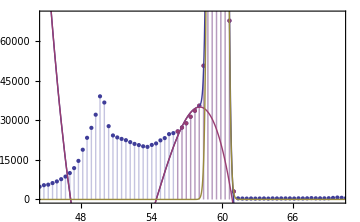

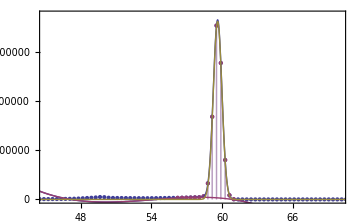

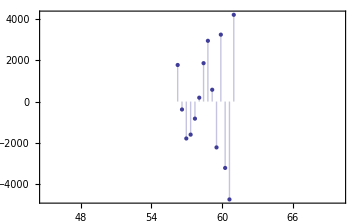

```mathematica
region={154,167};
Clear[a,b,c,d,mu,sigma,p]
viewingregion={50,200};viewingrange={45,70};imagesize=Medium;fontsize=12;theme="Classic";

guess={{a,361},{b,-61524},{c,3473469},{d,-65035121},{mu,59.6},{sigma,0.37},{p,670000}};

k=1;
cubic[k]=NonlinearModelFit[data[k][[region[[1]];;region[[2]],{2,3}]],a x^3+b x^2+c x+d+F[x,mu,sigma,p],guess,x];

cubic[k]["ParameterTable"]
cubicparams[k]=cubic[k]["BestFitParameters"][[All,2]];

Show[ListPlot[{data[k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[k][[region[[1]];;region[[2]],{2,3}]]},Filling->Axis,PlotRange->All,PlotTheme->theme],Plot[{cubic[k]["BestFit"],cubicparams[k][[1]]x^3+cubicparams[k][[2]]x^2+cubicparams[k][[3]]x+cubicparams[k][[4]],F[x,cubicparams[k][[-3]],cubicparams[k][[-2]],cubicparams[k][[-1]]]},{x,-10,100},PlotTheme->theme],PlotRange->{viewingrange,{0,70000}},Frame->{{True,False},{True,False}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]

Show[ListPlot[{data[k][[viewingregion[[1]];;viewingregion[[2]],{2,3}]],data[k][[region[[1]];;region[[2]],{2,3}]]},Filling->Axis,PlotRange->All,PlotTheme->theme],Plot[{cubic[k]["BestFit"],cubicparams[k][[1]]x^3+cubicparams[k][[2]]x^2+cubicparams[k][[3]]x+cubicparams[k][[4]],F[x,cubicparams[k][[-3]],cubicparams[k][[-2]],cubicparams[k][[-1]]]},{x,-10,100},PlotTheme->theme],PlotRange->{viewingrange,{0,3000000}},Frame->{{True,False},{True,False}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]

ListPlot[Join[Table[{energy[k][[1]]+energy[k][[2]](i-1)},{i,region[[1]],region[[2]]}],Transpose[{cubic[k]["FitResiduals"]}],2],Filling->Axis,Frame->{{True,False},{True,False}},FrameTicks->{{True,False},{True,False}},Axes->True,PlotRange->{viewingrange,All},PlotTheme->theme,ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]
```

## Gaussian Fits

```mathematica
mu={24.1,26.4,51.6,49.6,56.7,58.6,59.6};
sigma={0.6,0.4,4.0,0.7,1.4,0.8,0.36};
a={5000,20000,18000,18000,16000,24000,2900000};
n=Length[mu];region={1,3000};
symbol={"μ","σ","a","I"};

For[k=1,k≤m,k++,
model[k]=NonlinearModelFit[data[k][[region[[1]];;region[[2]],{2,3}]],G[x,Table[Symbol["mu"<>ToString[i]],{i,1,n}],Table[Symbol["sigma"<>ToString[i]],{i,1,n}],Table[Symbol["a"<>ToString[i]],{i,1,n}]],Join[Table[{Symbol["mu"<>ToString[i]],mu[[i]]},{i,1,n}],Table[{Symbol["sigma"<>ToString[i]],sigma[[i]]},{i,1,n}],Table[{Symbol["a"<>ToString[i]],a[[i]]},{i,1,n}]],x];
params[k]=model[k]["BestFitParameters"][[All,2]];
paramerrors[k]=model[k]["ParameterErrors"];

modeldata=Table[err[F,{i,0},{params[k][[n]],paramerrors[k][[n]]},{params[k][[2n]],paramerrors[k][[2n]]},{params[k][[3n]],paramerrors[k][[3n]]}],{i,Table[data[k][[i[[1]],2]],{i,Position[data[k][[;;200,2]],_?(params[k][[n]]-2*fwhm[params[k][[2n]]]<#<params[k][[n]]+2*fwhm[params[k][[2n]]]&)]}]}];
intensity[k]={Total[modeldata[[All,1]]*energy[k][[2]]],Sqrt[Total[(modeldata[[All,2]]*energy[k][[2]])^2]]};
Print[TableForm[Insert[Insert[

Table[{symbol[[i/n]],params[k][[i]],paramerrors[k][[i]],100*paramerrors[k][[i]]/params[k][[i]]},{i,{n,2n,3n}}],

Join[{symbol[[4]]},intensity[k],{100*intensity[k][[2]]/intensity[k][[1]]}],4]
,{{},{"Value"},{"Error"},{"Percent Error"}},1]]];
];
```

| Value | Error | Percent Error
μ | 59.6266 | 0.000140453 | 0.000235554
σ | 0.366736 | 0.000252425 | 0.0688301
a | 2.90504×10^6 | 3389.4 | 0.116673
I | 2.6705×10^6 | 1897.26 | 0.0710452

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

| Value | Error | Percent Error
μ | 59.6338 | 0.00012363 | 0.000207315
σ | 0.365779 | 0.000233078 | 0.0637212
a | 2.83578×10^6 | 3038.62 | 0.107153
I | 2.60003×10^6 | 1698.53 | 0.0653273

| Value | Error | Percent Error
μ | 59.6437 | 0.000150192 | 0.000251815
σ | 0.365785 | 0.000277041 | 0.0757387
a | 2.64429×10^6 | 3539.41 | 0.133851
I | 2.42451×10^6 | 1957.19 | 0.0807249

| Value | Error | Percent Error
μ | 59.6361 | 0.000146934 | 0.000246384
σ | 0.36568 | 0.000272427 | 0.0744988
a | 2.56942×10^6 | 3374.44 | 0.131331
I | 2.35517×10^6 | 1866.6 | 0.0792554

| Value | Error | Percent Error
μ | 59.6603 | 0.000141167 | 0.000236618
σ | 0.365971 | 0.000258453 | 0.070621
a | 2.88027×10^6 | 3444.76 | 0.119598
I | 2.64222×10^6 | 1924.22 | 0.0728258

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

| Value | Error | Percent Error
μ | 59.6407 | 0.00012897 | 0.000216245
σ | 0.365488 | 0.00024468 | 0.0669459
a | 2.80719×10^6 | 3274.35 | 0.116642
I | 2.57177×10^6 | 1813.91 | 0.0705313

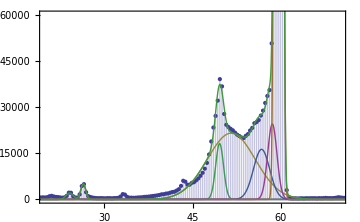
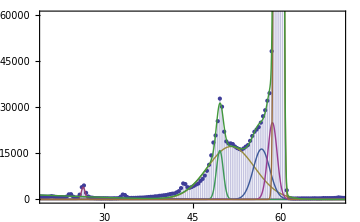
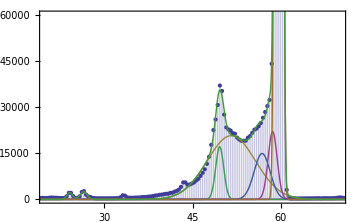
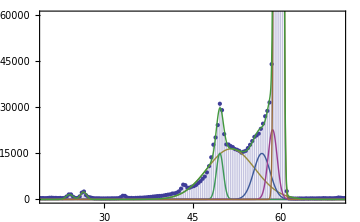
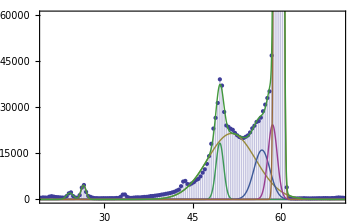
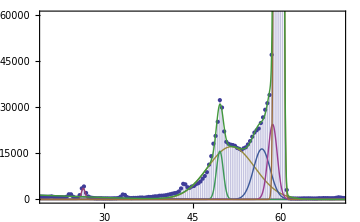
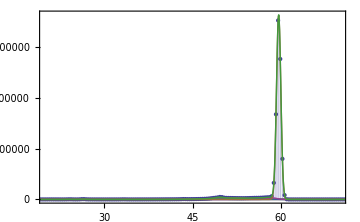
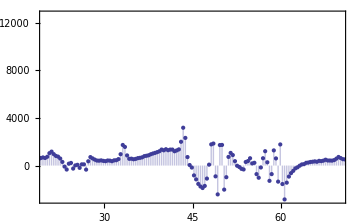
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- -Graphics- | -Graphics- -Graphics- | -Graphics- -Graphics- | -Graphics- -Graphics- | -Graphics- -Graphics- | -Graphics- -Graphics-

```mathematica
viewingrange={20,70};
theme="Classic";imagesize=Medium;fontsize=12;

Grid[Transpose[Table[{Show[ListPlot[data[k][[region[[1]];;region[[2]],{2,3}]],Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[k][[i]],params[k][[i+n]],params[k][[i+2n]]],{i,1,n}],{G[x,params[k][[;;n]],params[k][[n+1;;2n]],params[k][[2n+1;;3n]]]}],{x,-10,200},PlotRange->All,PlotTheme->theme],Frame->{{True,False},{True,False}},PlotRange->{viewingrange,{0,60000}},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}],

Show[ListPlot[data[k][[region[[1]];;region[[2]],{2,3}]],Filling->Bottom,PlotTheme->theme,PlotRange->All],Plot[Evaluate@Join[Table[F[x,params[k][[i]],params[k][[i+n]],params[k][[i+2n]]],{i,1,n}],{G[x,params[k][[;;n]],params[k][[n+1;;2n]],params[k][[2n+1;;3n]]]}],{x,-10,200},PlotRange->All,PlotTheme->theme],Frame->{{True,False},{True,False}},PlotRange->{viewingrange,All},ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]

ListPlot[Join[Table[{energy[k][[1]]+energy[k][[2]](i-1)},{i,region[[1]],region[[2]]}],Transpose[{model[k]["FitResiduals"]}],2],Filling->Axis,Frame->{{True,False},{True,False}},FrameTicks->{{True,False},{True,False}},Axes->True,PlotRange->{viewingrange,All},PlotTheme->theme,ImageSize->imagesize,BaseStyle->{FontSize->fontsize}]},{k,1,m}]]]
```

```mathematica
coeff[counts1_,counts3_,thickness_]:=(-Log[counts3/counts1])/thickness;
runs={"Source 1","Source 2","Thick 1","Thick 2","Thin 1", "Thin 2"};
thickness={40,0.01};

Print[TableForm[Insert[Table[Join[{runs[[i]]},intensity[i],{100*intensity[i][[2]]/intensity[i][[1]]}],{i,1,m}],{{},{"Intensity"},{"Error"},"Percent Error"},1]]]

Print["\nTrial 1"]
atten=err[coeff,intensity[1],intensity[3],thickness];
Print["attenuation coefficient = ",Join[atten,{100*atten[[2]]/atten[[1]]}]]
thin=err[coeff,intensity[1],intensity[5],atten];Print["thin foil measurement = ",Join[thin,{100*thin[[2]]/thin[[1]]}]]

Print["\nTrial 2"]
atten=err[coeff,intensity[2],intensity[4],thickness];
Print["attenuation coefficient = ",Join[atten,{100*atten[[2]]/atten[[1]]}]]
thin=err[coeff,intensity[2],intensity[6],atten];Print["thin foil measurement = ",Join[thin,{100*thin[[2]]/thin[[1]]}]]
```

| Intensity | Error | Percent Error
Source 1 | 2.6705×10^6 | 1897.26 | 0.0710452
Source 2 | 2.60003×10^6 | 1698.53 | 0.0653273
Thick 1 | 2.42451×10^6 | 1957.19 | 0.0807249
Thick 2 | 2.35517×10^6 | 1866.6 | 0.0792554
Thin 1 | 2.64222×10^6 | 1924.22 | 0.0728258
Thin 2 | 2.57177×10^6 | 1813.91 | 0.0705313

Trial 1

attenuation coefficient = {0.00241588,0.0000268907,1.11308}

thin foil measurement = {4.40628,0.423977,9.62211}

Trial 2

attenuation coefficient = {0.00247274,0.0000256846,1.03871}

thin foil measurement = {4.41929,0.391488,8.85863}